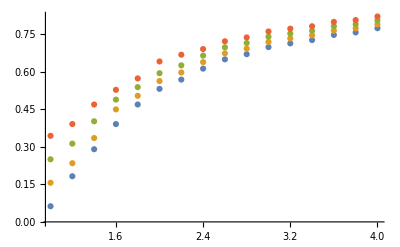

```mathematica
b={{1,2/(1×32)}, {1.2,7/(1.2×32)},{1.4,13/(1.4×32)},{1.6,20/(1.6×32)}, {1.8,27/(1.8×32)},{2,34/(2×32)},{2.2,40/(2.2×32)},{2.4,47/(2.4×32)},{2.6,54/(2.6×32)},{2.8,60/(2.8×32)},{3,67/(3×32)},{3.2,73/(3.2×32)},{3.4,79/(3.4×32)},{3.6,86/(3.6×32)},{3.8,92/(3.8×32)},{4,99/(4×32)}};
b2={{1,5/(1×32)}, {1.2,9/(1.2×32)},{1.4,15/(1.4×32)},{1.6,23/(1.6×32)}, {1.8,29/(1.8×32)},{2,36/(2×32)},{2.2,42/(2.2×32)},{2.4,49/(2.4×32)},{2.6,56/(2.6×32)},{2.8,62/(2.8×32)},{3,69/(3×32)},{3.2,75/(3.2×32)},{3.4,81/(3.4×32)},{3.6,88/(3.6×32)},{3.8,94/(3.8×32)},{4,101/(4×32)}};
b3={{1,8/(1×32)}, {1.2,12/(1.2×32)},{1.4,18/(1.4×32)},{1.6,25/(1.6×32)}, {1.8,31/(1.8×32)},{2,38/(2×32)},{2.2,44/(2.2×32)},{2.4,51/(2.4×32)},{2.6,58/(2.6×32)},{2.8,64/(2.8×32)},{3,71/(3×32)},{3.2,77/(3.2×32)},{3.4,83/(3.4×32)},{3.6,90/(3.6×32)},{3.8,96/(3.8×32)},{4,103/(4×32)}};
b4={{1,11/(1×32)}, {1.2,15/(1.2×32)},{1.4,21/(1.4×32)},{1.6,27/(1.6×32)}, {1.8,33/(1.8×32)},{2,41/(2×32)},{2.2,47/(2.2×32)},{2.4,53/(2.4×32)},{2.6,60/(2.6×32)},{2.8,66/(2.8×32)},{3,73/(3×32)},{3.2,79/(3.2×32)},{3.4,85/(3.4×32)},{3.6,92/(3.6×32)},{3.8,98/(3.8×32)},{4,105/(4×32)}};
ListPlot[{b,b2,b3,b4}]
```

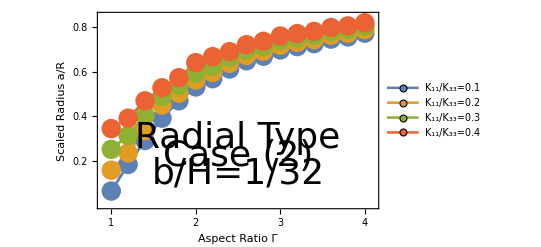

```mathematica
ListPlot[{b,b2,b3,b4},PlotStyle->{Thickness[0.005]},PlotMarkers->{Graphics[{Disk[]},ImageSize->20],Graphics[{Disk[]},ImageSize->20]},Joined->{True, True,True, True}, Frame->{True, True, True, True}, FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{1,1.5,2,2.5,3,3.5,4},None}}, PlotRange->{{0.9,4.1},{0,0.85}},FrameLabel->{{"Scaled Radius a/R", None},{"Aspect Ratio Γ", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=0.2","K_11/K_33=0.3","K_11/K_33=0.4"},LegendMarkers->{{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20},{Graphics[Disk[]],20}}],{Right, Bottom}],Epilog->{Text[Style["Radial Type",Directive[Black,36]],{2.5,0.3}],Text[Style["Case (2)",Directive[Black,36]],{2.5,0.22}],Text[Style["b/H=1/32",Directive[Black,36]],{2.5,0.14}]}]
```